```mathematica
<<"/Users/lucaarnaboldi/Desktop/staircase-ss/mathematica/Isserlis.m"
```

```mathematica
Omega
```

{{ω[1,1],ω[1,2],ω[1,3],ω[1,4],ω[1,5],ω[1,6],0},{ω[1,2],ω[2,2],ω[2,3],ω[2,4],ω[2,5],ω[2,6],0},{ω[1,3],ω[2,3],ω[3,3],ω[3,4],ω[3,5],ω[3,6],0},{ω[1,4],ω[2,4],ω[3,4],ω[4,4],ω[4,5],ω[4,6],0},{ω[1,5],ω[2,5],ω[3,5],ω[4,5],ω[5,5],ω[5,6],0},{ω[1,6],ω[2,6],ω[3,6],ω[4,6],ω[5,6],ω[6,6],0},{0,0,0,0,0,0,Δ}}

```mathematica
(*I2noise = Expand[(2*lf[1])*(2*lf[2])]*)
I2noise = Expand[(3*lf[1]^2-3)*(3*lf[2]^2-3)]
(**)
(*I2 = Expand[(lf[1])*(lf[2])]*)
(*I2 = Expand[(lf[1]^2-1)*(lf[2]^2-1)]*)
I2 = Expand[(lf[1]^3-3*lf[1])*(lf[2]^3-3*lf[2])]
(*I2=Expand[(lf[1]^4-6*lf[1]^2+3)*(lf[2]^4-6*lf[2]^2+3)]*)
(**)
(*I3 = Expand[(1)*lf[2]*(lf[3])]*)
(*I3 = Expand[2*lf[1]*lf[2]*(lf[3]^2-1)]*)
I3 = Expand[(3*lf[1]^2-3)*lf[2]*(lf[3]^3-3*lf[3])]
(*I3 = Expand[(4*lf[1]^3-12*lf[1])*lf[2]*(lf[3]^4-6*lf[3]^2+3)]*)
(*I3 = Expand[(5*lf[1]^4-30*lf[1]^2+15)*lf[2]*(lf[3]^5-10*lf[3]^3+15*lf[3])]*)
(*I3 = Expand[(6*lf[1]^5-60*lf[1]^3+90*lf[1])*lf[2]*(lf[3]^6-15*lf[3]^4+45*lf[3]^2-15)]*)
(**)
(*I4 = Expand[(1)*(1)*(lf[3])*(lf[4])]*)
(*I4 = Expand[(2*lf[1])*(2*lf[2])*(lf[3]^2-1)*(lf[4]^2-1)]*)
I4 = Expand[(3*lf[1]^2-3)*(3*lf[2]^2-3)*(lf[3]^3-3*lf[3])*(lf[4]^3-3*lf[4])]
(*I4 = Expand[(4*lf[1]^3-12*lf[1])*(4*lf[2]^3-12*lf[2])*(lf[3]^4-6*lf[3]^2+3)*(lf[4]^4-6*lf[4]^2+3)]*)
(*I4 = Expand[(5*lf[1]^4-30*lf[1]^2+15)*(5*lf[2]^4-30*lf[2]^2+15)*(lf[3]^5-10*lf[3]^3+15*lf[3])*(lf[4]^5-10*lf[4]^3+15*lf[4])]*)
(*I4 = Expand[(6*lf[1]^5-60*lf[1]^3+90*lf[1])*(6*lf[2]^5-60*lf[2]^3+90*lf[2])*(lf[3]^6-15*lf[3]^4+45*lf[3]^2-15)*(lf[4]^6-15*lf[4]^4+45*lf[4]^2-15)]*)
```

4 λ[1] λ[2]

1-λ[1]^2-λ[2]^2+λ[1]^2 λ[2]^2

-2 λ[1] λ[2]+2 λ[1] λ[2] λ[3]^2

4 λ[1] λ[2]-4 λ[1] λ[2] λ[3]^2-4 λ[1] λ[2] λ[4]^2+4 λ[1] λ[2] λ[3]^2 λ[4]^2

```mathematica
Psit =IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->m, ω[1,3]->m,ω[2,2]->ρ,ω[2,3]->ρ,ω[3,3]->ρ} ;
Psis= IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->m, ω[1,3]->q,ω[2,2]->ρ,ω[2,3]->m,ω[3,3]->q} ;
PhiHDtt = IsserlisTheorem[I4] /. {ω[1,1]->q, ω[1,2]->q, ω[1,3]->m,ω[1,4]->m,ω[2,2]->q,ω[2,3]->m,ω[2,4]->m,ω[3,3]->ρ,ω[3,4]->ρ,ω[4,4]->ρ} ;
PhiHDss = IsserlisTheorem[I4] /. {ω[1,1]->q, ω[1,2]->q, ω[1,3]->q,ω[1,4]->q,ω[2,2]->q,ω[2,3]->q,ω[2,4]->q,ω[3,3]->q,ω[3,4]->q,ω[4,4]->q} ;
PhiHDts = IsserlisTheorem[I4] /. {ω[1,1]->q, ω[1,2]->q, ω[1,3]->q,ω[1,4]->m,ω[2,2]->q,ω[2,3]->q,ω[2,4]->m,ω[3,3]->q,ω[3,4]->m,ω[4,4]->ρ} ;
PhiHDnoise = IsserlisTheorem[I2noise] /. {ω[1,1]->q,ω[1,2]->m,ω[2,2]->ρ};
PhiGFt =IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->q, ω[1,3]->m,ω[2,2]->q,ω[2,3]->m,ω[3,3]->ρ} ;
PhiGFs= IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->q, ω[1,3]->q,ω[2,2]->q,ω[2,3]->q,ω[3,3]->q} ;
Riskss =IsserlisTheorem[I2] /.{ω[1,1]->q,ω[1,2]->q,ω[2,2]->q};
Risktt = IsserlisTheorem[I2] /.{ω[1,1]->ρ,ω[1,2]->ρ,ω[2,2]->ρ};
Riskts = IsserlisTheorem[I2] /.{ω[1,1]->q,ω[1,2]->m,ω[2,2]->ρ};
Pinv = 1/ρ;
Qorthinv = 1/(q-m^2/ρ);
GFM = FullSimplify[(Psit-Psis)];
GFQ = FullSimplify[(PhiGFt-PhiGFs)];
GFQorth = FullSimplify[GFstudent - m*Pinv*GFteacher];
HDQ = (PhiHDtt+PhiHDss-2*PhiHDts+Δ*PhiHDnoise);
mUpdate =γ*GFM
qUpdate = FullSimplify[2*γ*GFQ+γ^2*1/α*HDterm+γ^2*(GFteacher*Pinv*GFteacher)+γ^2*(GForth*Qorthinv*GForth)]
PopRisk = 1/2*(Riskss +Risktt-2*Riskts)
```

6 m γ (-q+ρ)

(4 γ (m γ Δ+2 m^2 (6 γ (-2 q+ρ)+α (1-6 q γ+4 γ ρ))+q (3 q^2 (5+3 α) γ-3 q (α+2 (1+α) γ ρ)+ρ (α+(3+α) γ ρ))))/α

1/2 (2-2 q+3 q^2-2 ρ+3 ρ^2-2 (1+2 m^2-q-ρ+q ρ))

```mathematica
mUpdateSpherical = Expand[FullSimplify[(mUpdate-m/2*qUpdate)/.{ρ->1,q->1}]]
```

4 m γ-4 m^3 γ-8 m γ^2+8 m^3 γ^2-(24 m γ^2)/α+(24 m^3 γ^2)/α-(2 m^2 γ^2 Δ)/α

1/2 (2-2 q+3 q^2-2 ρ+3 ρ^2-2 (1-q+2 x^2-ρ+q ρ))

0.

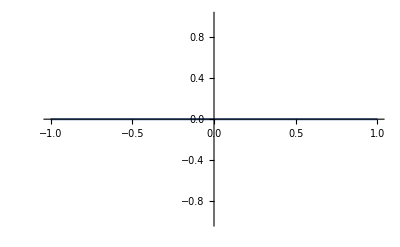

```mathematica
functionMUpdateSpherical[x_] = mUpdateSpherical /. {m->x, γ->0,Δ->.001};
functionPopRisk[x_] =PopRisk /.{m ->x,Δ->0.001}
EffectivePontentialSGD[m_]= -Integrate[functionMUpdateSpherical[x], {x,1,m}]
Plot[{EffectivePontentialSGD[m],functionPopRisk[m]},{m,-1,1}]
```

```mathematica
IsserlisTheorem[I4]
```

4 ω[1,2]-8 ω[1,3] ω[2,3]-8 ω[1,4] ω[2,4]-4 ω[1,2] ω[3,3]+8 ω[1,4] ω[2,4] ω[3,3]+16 ω[1,4] ω[2,3] ω[3,4]+16 ω[1,3] ω[2,4] ω[3,4]+8 ω[1,2] ω[3,4]^2-4 ω[1,2] ω[4,4]+8 ω[1,3] ω[2,3] ω[4,4]+4 ω[1,2] ω[3,3] ω[4,4]

```mathematica
IsserlisTheorem[81 lf[3] lf[4]-81 lf[1]^2 lf[3] lf[4]-81 lf[2]^2 lf[3] lf[4]+81 lf[1]^2 lf[2]^2 lf[3] lf[4]-27 lf[3]^3 lf[4]+27 lf[1]^2 lf[3]^3 lf[4]+27 lf[2]^2 lf[3]^3 lf[4]-27 lf[1]^2 lf[2]^2 lf[3]^3 lf[4]-27 lf[3] lf[4]^3+27 lf[1]^2 lf[3] lf[4]^3+27 lf[2]^2 lf[3] lf[4]^3-27 lf[1]^2 lf[2]^2 lf[3] lf[4]^3+9 lf[3]^3 lf[4]^3-9 lf[1]^2 lf[3]^3 lf[4]^3-9 lf[2]^2 lf[3]^3 lf[4]^3+9 lf[1]^2 lf[2]^2 lf[3]^3 lf[4]^3]
```

-162 ω[1,3] ω[1,4]+162 ω[1,3] ω[1,4] ω[2,2]+324 ω[1,2] ω[1,4] ω[2,3]-324 ω[1,3] ω[1,4] ω[2,3]^2+324 ω[1,2] ω[1,3] ω[2,4]-162 ω[2,3] ω[2,4]+162 ω[1,1] ω[2,3] ω[2,4]-324 ω[1,3]^2 ω[2,3] ω[2,4]-324 ω[1,4]^2 ω[2,3] ω[2,4]-324 ω[1,3] ω[1,4] ω[2,4]^2+162 ω[1,3] ω[1,4] ω[3,3]-162 ω[1,3] ω[1,4] ω[2,2] ω[3,3]-324 ω[1,2] ω[1,4] ω[2,3] ω[3,3]-324 ω[1,2] ω[1,3] ω[2,4] ω[3,3]+162 ω[2,3] ω[2,4] ω[3,3]-162 ω[1,1] ω[2,3] ω[2,4] ω[3,3]+324 ω[1,4]^2 ω[2,3] ω[2,4] ω[3,3]+324 ω[1,3] ω[1,4] ω[2,4]^2 ω[3,3]+81 ω[3,4]-81 ω[1,1] ω[3,4]+162 ω[1,2]^2 ω[3,4]+162 ω[1,3]^2 ω[3,4]+162 ω[1,4]^2 ω[3,4]-81 ω[2,2] ω[3,4]+81 ω[1,1] ω[2,2] ω[3,4]-162 ω[1,3]^2 ω[2,2] ω[3,4]-162 ω[1,4]^2 ω[2,2] ω[3,4]-648 ω[1,2] ω[1,3] ω[2,3] ω[3,4]+162 ω[2,3]^2 ω[3,4]-162 ω[1,1] ω[2,3]^2 ω[3,4]+324 ω[1,4]^2 ω[2,3]^2 ω[3,4]-648 ω[1,2] ω[1,4] ω[2,4] ω[3,4]+1296 ω[1,3] ω[1,4] ω[2,3] ω[2,4] ω[3,4]+162 ω[2,4]^2 ω[3,4]-162 ω[1,1] ω[2,4]^2 ω[3,4]+324 ω[1,3]^2 ω[2,4]^2 ω[3,4]-81 ω[3,3] ω[3,4]+81 ω[1,1] ω[3,3] ω[3,4]-162 ω[1,2]^2 ω[3,3] ω[3,4]-162 ω[1,4]^2 ω[3,3] ω[3,4]+81 ω[2,2] ω[3,3] ω[3,4]-81 ω[1,1] ω[2,2] ω[3,3] ω[3,4]+162 ω[1,4]^2 ω[2,2] ω[3,3] ω[3,4]+648 ω[1,2] ω[1,4] ω[2,4] ω[3,3] ω[3,4]-162 ω[2,4]^2 ω[3,3] ω[3,4]+162 ω[1,1] ω[2,4]^2 ω[3,3] ω[3,4]-324 ω[1,3] ω[1,4] ω[3,4]^2+324 ω[1,3] ω[1,4] ω[2,2] ω[3,4]^2+648 ω[1,2] ω[1,4] ω[2,3] ω[3,4]^2+648 ω[1,2] ω[1,3] ω[2,4] ω[3,4]^2-324 ω[2,3] ω[2,4] ω[3,4]^2+324 ω[1,1] ω[2,3] ω[2,4] ω[3,4]^2+54 ω[3,4]^3-54 ω[1,1] ω[3,4]^3+108 ω[1,2]^2 ω[3,4]^3-54 ω[2,2] ω[3,4]^3+54 ω[1,1] ω[2,2] ω[3,4]^3+162 ω[1,3] ω[1,4] ω[4,4]-162 ω[1,3] ω[1,4] ω[2,2] ω[4,4]-324 ω[1,2] ω[1,4] ω[2,3] ω[4,4]+324 ω[1,3] ω[1,4] ω[2,3]^2 ω[4,4]-324 ω[1,2] ω[1,3] ω[2,4] ω[4,4]+162 ω[2,3] ω[2,4] ω[4,4]-162 ω[1,1] ω[2,3] ω[2,4] ω[4,4]+324 ω[1,3]^2 ω[2,3] ω[2,4] ω[4,4]-162 ω[1,3] ω[1,4] ω[3,3] ω[4,4]+162 ω[1,3] ω[1,4] ω[2,2] ω[3,3] ω[4,4]+324 ω[1,2] ω[1,4] ω[2,3] ω[3,3] ω[4,4]+324 ω[1,2] ω[1,3] ω[2,4] ω[3,3] ω[4,4]-162 ω[2,3] ω[2,4] ω[3,3] ω[4,4]+162 ω[1,1] ω[2,3] ω[2,4] ω[3,3] ω[4,4]-81 ω[3,4] ω[4,4]+81 ω[1,1] ω[3,4] ω[4,4]-162 ω[1,2]^2 ω[3,4] ω[4,4]-162 ω[1,3]^2 ω[3,4] ω[4,4]+81 ω[2,2] ω[3,4] ω[4,4]-81 ω[1,1] ω[2,2] ω[3,4] ω[4,4]+162 ω[1,3]^2 ω[2,2] ω[3,4] ω[4,4]+648 ω[1,2] ω[1,3] ω[2,3] ω[3,4] ω[4,4]-162 ω[2,3]^2 ω[3,4] ω[4,4]+162 ω[1,1] ω[2,3]^2 ω[3,4] ω[4,4]+81 ω[3,3] ω[3,4] ω[4,4]-81 ω[1,1] ω[3,3] ω[3,4] ω[4,4]+162 ω[1,2]^2 ω[3,3] ω[3,4] ω[4,4]-81 ω[2,2] ω[3,3] ω[3,4] ω[4,4]+81 ω[1,1] ω[2,2] ω[3,3] ω[3,4] ω[4,4]

```mathematica
FortranForm[IsserlisTheorem[I2noise]/.{ω->c}]
```

4*c(1,2)

```mathematica
IsserlisTheorem(9 - 9*lf(1)**2 - 9*lf(2)**2 + 9*lf(1)**2*lf(2)**2)
```

IsserlisTheorem (9-9 λ 1**2-9 λ 2**2+9 λ^2 1**2 2**2)

```mathematica
FortranForm[IsserlisTheorem[I2]/.{ω->c}]
```

1 - c(1,1) + 2*c(1,2)**2 - c(2,2) + c(1,1)*c(2,2)

```mathematica
IsserlisTheorem(9 - 18*lf(1)**2 + 3*lf(1)**4 - 18*lf(2)**2 + 
     -   36*lf(1)**2*lf(2)**2 - 6*lf(1)**4*lf(2)**2 + 3*lf(2)**4 - 
     -   6*lf(1)**2*lf(2)**4 + lf(1)**4*lf(2)**4)
```

IsserlisTheorem (9-18 λ 1**2+3 λ 1**4-18 λ 2**2-36 λ^2 1**2 2**2-6 λ^2 1**4 2**2+3 λ 2**4+6 λ^2 1**2 2**4+λ^2 1**4 2**4)

```mathematica
FortranForm[IsserlisTheorem[I3]/.{ω->c}]
```

-2*c(1,2) + 4*c(1,3)*c(2,3) + 2*c(1,2)*c(3,3)

```mathematica
IsserlisTheorem(9*lf(2)*lf(3) - 9*lf(1)**2*lf(2)*lf(3) - 
     -   3*lf(2)*lf(3)**3 + 3*lf(1)**2*lf(2)*lf(3)**3)
```

IsserlisTheorem (54 λ^2-54 λ^3 1**2+6 λ^2 3**3+6 λ^3 1**2 3**3)

```mathematica
FortranForm[IsserlisTheorem[I4]/.{ω->c}]
```

4*c(1,2) - 8*c(1,3)*c(2,3) - 8*c(1,4)*c(2,4) - 4*c(1,2)*c(3,3) + 
     -  8*c(1,4)*c(2,4)*c(3,3) + 16*c(1,4)*c(2,3)*c(3,4) + 
     -  16*c(1,3)*c(2,4)*c(3,4) + 8*c(1,2)*c(3,4)**2 - 4*c(1,2)*c(4,4) + 
     -  8*c(1,3)*c(2,3)*c(4,4) + 4*c(1,2)*c(3,3)*c(4,4)

```mathematica
IsserlisTheorem(81*lf(3)*lf(4) - 81*lf(1)**2*lf(3)*lf(4) - 
     -   81*lf(2)**2*lf(3)*lf(4) + 
     -   81*lf(1)**2*lf(2)**2*lf(3)*lf(4) - 27*lf(3)**3*lf(4) + 
     -   27*lf(1)**2*lf(3)**3*lf(4) + 27*lf(2)**2*lf(3)**3*lf(4) - 
     -   27*lf(1)**2*lf(2)**2*lf(3)**3*lf(4) - 27*lf(3)*lf(4)**3 + 
     -   27*lf(1)**2*lf(3)*lf(4)**3 + 27*lf(2)**2*lf(3)*lf(4)**3 - 
     -   27*lf(1)**2*lf(2)**2*lf(3)*lf(4)**3 + 9*lf(3)**3*lf(4)**3 - 
     -   9*lf(1)**2*lf(3)**3*lf(4)**3 - 
     -   9*lf(2)**2*lf(3)**3*lf(4)**3 + 
     -   9*lf(1)**2*lf(2)**2*lf(3)**3*lf(4)**3)
```

IsserlisTheorem (972 λ^2-972 λ^3 1**2+972 λ^3 2**2-972 λ^4 1**2 2**2-108 λ^2 3**3-108 λ^3 1**2 3**3+108 λ^3 2**2 3**3+108 λ^4 1**2 2**2 3**3-81 λ^2 4**3-81 λ^3 1**2 4**3+81 λ^3 2**2 4**3+81 λ^4 1**2 2**2 4**3+9 λ^2 3**3 4**3+9 λ^3 1**2 3**3 4**3+9 λ^3 2**2 3**3 4**3-9 λ^4 1**2 2**2 3**3 4**3)